```mathematica
ClearAll[x,y,z,testData,testdata,intData2, intData3]
```

```mathematica
flukaData=Import["/home/hovanes/klcps_31b.bnn.lis.table.csv","CSV"]
```

{{0.0125,-3.11978,0.25,38.0905},{0.0125,-3.11978,0.75,72.645},{0.0125,-3.11978,1.25,126.035},{0.0125,-3.11978,1.75,179.89},{0.0125,-3.11978,2.25,254.1},{0.0125,-3.11978,2.75,354.11},{0.0125,-3.11978,3.25,411.005},{0.0125,-3.11978,3.75,504.25},{0.0125,-3.11978,4.25,575.85},6497262,{5.9875,-3.1634,89.75,0.000292525},{5.9875,-3.1634,90.25,0.00150975},{5.9875,-3.1634,90.75,0.00231685},{5.9875,-3.1634,91.25,0.0016567},{5.9875,-3.1634,91.75,0.0043239},{5.9875,-3.1634,92.25,0.0013032},{5.9875,-3.1634,92.75,0.00092605},{5.9875,-3.1634,93.25,0.000234535},{5.9875,-3.1634,93.75,0.0018861}}
 |  |  |  |

```mathematica
flukaDataIP=Interpolation[flukaData]
```

InterpolatingFunction[{{0.0125, 5.9875}, {-5.21417, 1.02538}, {0.25, 93.75}}, <>]

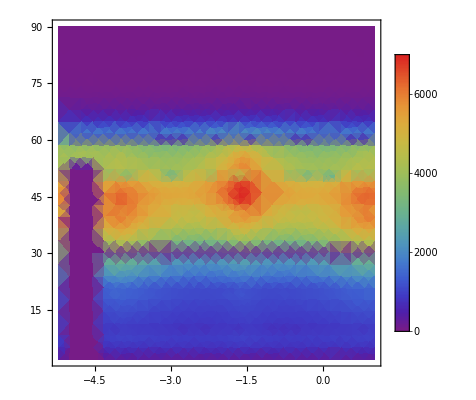

```mathematica
DensityPlot[flukaDataIP[0.026,y,z], {y,-Pi,+Pi}, {z,2, 90},PlotRange->Full,ColorFunction->{"Rainbow"},PlotLegends->Automatic,ScalingFunctions->{Identity,Identity,Identity}]
```

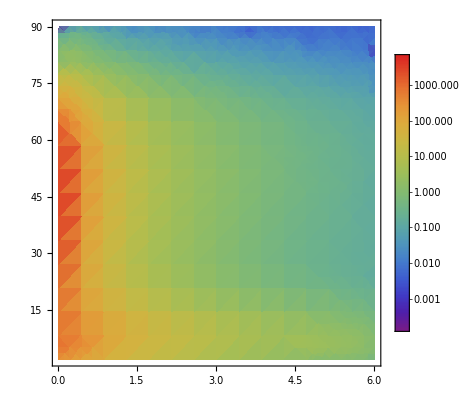

```mathematica
DensityPlot[flukaDataIP[x,-1.5,z], {x,-Pi, +Pi}, {z,2, 90},PlotRange->Full,ColorFunction->{"Rainbow"},PlotLegends->Automatic,ScalingFunctions->{Identity,Identity,"Log"}]
```

```mathematica
Export["/home/hovanes/klcps_31b.m" , flukaDataIP]
```